```mathematica
loca="/Users/abouchakra/Dropbox/Uoft/UOFT/projects/3-Cell_Cycle_Gene_Length_Theory/model_driven_theory/2019/dataR"
```

/Users/abouchakra/Dropbox/Uoft/UOFT/projects/3-Cell_Cycle_Gene_Length_Theory/model_driven_theory/2019/dataR

```mathematica
tsne1=Flatten[{Drop[Import[loca<>"/clusters_tsne-100-rp1--5-52-"<>ToString[#]<>"-1.dat"],1]}&/@{0,0.25,0.5,1,2,3},1];
```

```mathematica
local="/Users/abouchakra/Dropbox/Uoft/UOFT/projects/3-Cell_Cycle_Gene_Length_Theory/model_driven_theory/2019"
SetDirectory[local]




incr={0,0.25,0.5,1,2,3}
rg=Range[100,100](*,10}*);
filename=Flatten[Table[
{"cellcycletheory-sc-"<>ToString[#]<>"-rp1--5-52.-11111-1-5-5-5-0-1-"<>ToString[incr]
(*"cellcycletheory-sc-"<>ToString[#]<>"-rp1--5-42.-1111-1-5-5-5-0-1-"<>ToString[incr]*)
}&/@rg,
{incr,{0,0.25,0.5,1,2,3}}]]
(*exports the files so R can use them to cluster*)
ccd1=ReadList[local<>"/data3D/"<>#<>"-0-0-0-0.5-5-2-2-1-2--1--2-0.01-0.01-0.3--1-0.dat"]&/@filename;
ccd=ccd1[[All,All,4]];
```

/Users/abouchakra/Dropbox/Uoft/UOFT/projects/3-Cell_Cycle_Gene_Length_Theory/model_driven_theory/2019

/Users/abouchakra/Dropbox/Uoft/UOFT/projects/3-Cell_Cycle_Gene_Length_Theory/model_driven_theory/2019

{0,0.25,0.5,1,2,3}

{cellcycletheory-sc-100-rp1--5-52.-11111-1-5-5-5-0-1-0,cellcycletheory-sc-100-rp1--5-52.-11111-1-5-5-5-0-1-0.25,cellcycletheory-sc-100-rp1--5-52.-11111-1-5-5-5-0-1-0.5,cellcycletheory-sc-100-rp1--5-52.-11111-1-5-5-5-0-1-1,cellcycletheory-sc-100-rp1--5-52.-11111-1-5-5-5-0-1-2,cellcycletheory-sc-100-rp1--5-52.-11111-1-5-5-5-0-1-3}

```mathematica
ff=Join[{4},Range[8,Length[ccd1[[1,1]]]]]
```

{4,8,9,10,11,12}

{{2},{2,4},{2,8},{2,48},{2,90},{2,122}}

{2,2}

{{{1,29}},{{1,29},{1,11,29,43}},{{1,29},{1,5,11,15,29,34,43,47}},{{1,29},{1,2,3,4,5,6,7,8,11,12,13,14,15,16,17,18,29,30,31,32,34,35,36,37,43,44,45,46,47,48,49,50,70,71,72,73,74,75,76,77,81,82,83,84,85,86,88,89}},{{1,29},{1,2,3,4,5,7,10,11,12,13,14,15,17,18,19,20,21,22,24,25,27,29,30,31,32,34,35,37,40,41,42,43,44,46,47,48,49,50,53,54,55,56,57,63,67,70,75,78,79,81,82,84,85,86,88,89,92,94,95,97,98,99,101,103,104,109,110,111,112,122,123,124,125,127,128,129,132,133,135,138,139,140,141,144,146,148,152,153,154,155}},{{1,29},{1,2,3,5,7,9,12,13,15,16,17,21,23,26,28,29,30,31,32,33,34,35,38,39,44,46,47,48,49,51,52,56,58,59,60,61,62,64,65,66,68,69,71,72,73,77,79,80,81,82,83,84,85,86,87,88,89,90,91,93,96,97,100,102,103,104,105,106,107,108,112,113,114,115,116,117,118,119,120,121,125,126,130,131,134,136,137,140,141,142,143,145,147,149,150,151,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180}}}

{-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-}

{RGBColor[0.3536047, 0.46289399999999997, 0.9223703],GrayLevel[0.85]}

-Graphics-

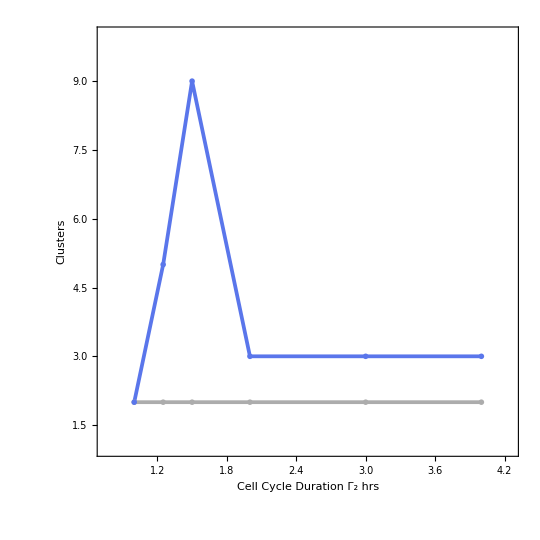

```mathematica
types=(SplitBy[Union[#],First])&/@ccd1[[All,All,ff]];
diversity=(Length/@#)&/@types
diversity[[1]]={2,2}
rp=Flatten[Table[StringJoin[ToString/@#[[i]]]->i,{i,1,Length[#]}]&/@{Union[Flatten[ccd1[[All,All,8;;All]],1]]}];
bc2=ReplaceAll[StringJoin[ToString/@#]&/@#,rp]&/@#&/@types[[All,All,All,2;;All]]
(*dc1=Table[DistributionChart[Reverse[bc2[[i]]],(*PlotRange->{{-0.15,2.05},{0.5,2}},*)ChartStyle->{ColorData["ThermometerColors"][0.15],LightGray},BarOrigin->Left,ChartElementFunction->"PointDensity",PlotLabel->Style["Med. Gene Length",12,Bold],BaseStyle->{12
,Black},FrameStyle->Directive[{Black,Thickness[0.005]}]],{i,Length[bc2]}]

*)
markers = {{-Graphics-, 0.04}, {-Graphics-, 0.04}, {-Graphics-, 0.05}, {-Graphics-, 0.04}};
markers={-Graphics-,-Graphics-,-Graphics-}
markers={-Graphics-,-Graphics-,-Graphics-}
{ColorData["ThermometerColors"][0.15],LightGray}
tt=TableForm[{Style[#,Lighter[Gray,0.35]]&/@{"1hr",1,2,5},Style[#,ColorData["ThermometerColors"][0.15]]&/@{"Γ_2",1,2,5}},TableHeadings->{None,{"Γ","L_1","L_G","G"}},TableSpacing->{1, 1}];
gnF2=ListPlot[Transpose[{{0,0.25,0.5,1,2,3}+1,#}]&/@Transpose[diversity],PlotRange->{{0.75,4.25},{-10,156}},FrameStyle->Directive[FontSize->25,Opacity[1],Black],FrameTicksStyle->Opacity[1],AspectRatio->1,Axes->False,Frame->True,
PlotStyle->{Directive[{Lighter[Gray,0.5],Thickness[0.005]}],Directive[{ColorData["ThermometerColors"][0.15],Thickness[0.005]}]},BaseStyle->{20},Joined->True,PlotMarkers->{markers,25},FrameTicks->{Automatic,{Automatic,Automatic}},FrameLabel->{"Cell Cycle Duration Γ_2 hrs","Transcriptome Diversity"},(*PlotLabel->"Same Number of Genes",*)
Epilog->{(*Text[Style[dc[[1]]ToString[gNmeMax[[1]] ] ,28],Center,{1.3,-10.1}],Text[Style[dc[[2]]ToString[gNmeMax[[2]] ] ,28],Center,{-1.3,-5.1}],*)
Text[Style["Γ_1 1.00 hr",Lighter[Gray,0.5]],Center,{-3.4,12}],
Text[Style["Γ_2 hrs",ColorData["ThermometerColors"][0.15]],Center,{-0.4,-3}],Text[tt,Center,{-0.4,-5}]},
(*PlotLegends->(*Placed[*)LineLegend[Style[dc[[#]]ToString[gNmeMax[[#]] ] ,16]&/@Range[1,Length[dc]]](*,{Center,{-0.2,0.2}}*)(*,{Center,Right}]*),*)ImageSize->540,ImagePadding->{{90, 10}, {Automatic, 10}}]
gnF3=ListPlot[Transpose[{{0,0.25,0.5,1,2,3}+1,#}]&/@{Table[2,{i,6}],(Length[Union[#]]&/@tsne1[[All,All,5]])},PlotRange->{{0.75,4.25},{1,10}},FrameStyle->Directive[FontSize->25,Opacity[1],Black],FrameTicksStyle->Opacity[1],AspectRatio->1,Axes->False,Frame->True,
PlotStyle->{Directive[{Lighter[Gray,0.35],Thickness[0.005]}],Directive[{ColorData["ThermometerColors"][0.15],Thickness[0.005]}]},BaseStyle->{20},Joined->True,PlotMarkers->{markers,25},FrameTicks->{Automatic,{Automatic,Automatic}},FrameLabel->{"Cell Cycle Duration Γ_2 hrs","Clusters"},(*PlotLabel->"Same Number of Genes",*)
Epilog->{(*Text[Style[dc[[1]]ToString[gNmeMax[[1]] ] ,28],Center,{1.3,-10.1}],Text[Style[dc[[2]]ToString[gNmeMax[[2]] ] ,28],Center,{-1.3,-5.1}],*)
(*Text[Style["Γ_1 1.00 hr",Lighter[Gray,0.35]],Center,{-3.4,12}],
Text[Style["Γ_2 hrs",ColorData["ThermometerColors"][0.15]],Center,{-0.4,-3}]*)(*Text["Parameters",Center,{-0.4,-18}],,Text[tt,Center,{-0.4,-4}]*)},
(*PlotLegends->(*Placed[*)LineLegend[Style[dc[[#]]ToString[gNmeMax[[#]] ] ,16]&/@Range[1,Length[dc]]](*,{Center,{-0.2,0.2}}*)(*,{Center,Right}]*),*)ImageSize->540,ImagePadding->{{80, 10}, {Automatic, 10}}]



(*(ReplacePart[#,rp]&/@Flatten[#[[All,All,2;;All]],1])&/@types*)
```

```mathematica
shad2=ListPlot[Transpose[{{1,2,3}+1,Take[#,-3]}]&/@{Table[2,{i,6}],(Length[Union[#]]&/@tsne1[[All,All,5]])},PlotRange->{{0.75,4.25},{0,10}},FrameStyle->Directive[FontSize->25,Opacity[1],Black],FrameTicksStyle->Opacity[1],AspectRatio->1,Axes->False,Frame->True,
PlotStyle->{Directive[{Pink,Thickness[0.005]}]},BaseStyle->{20},Joined->False,PlotMarkers->{markers,25},FrameTicks->{Automatic,{Automatic,Automatic}},FrameLabel->{"Cell Cycle Duration Γ_2 hrs","Clusters"},(*PlotLabel->"Same Number of Genes",*)
Epilog->{(*Text[Style["Inactive Filter",Pink],Center,{-1.65,14}],*)Text["Parameters",Center,{-1.65,-18}],Text[tt,Center,{-1.3,-4}]},ImageSize->540,ImagePadding->{{80, 10}, {Automatic, 10}}]
```

-Graphics-

```mathematica
shad=ListPlot[{{{0.93,0.75},{1.08,0.75}},{{1.7,0.75},{2,0.75}},{{2,0.75},{2.65,0.75}},{{3.35,0.75},{4,0.75}}},PlotRange->{{0.75,4.25},{0,10}},FrameStyle->Directive[FontSize->25,Opacity[1],Black],FrameTicksStyle->Opacity[1],AspectRatio->1/1.5,Axes->False,Frame->True,
PlotStyle->{Directive[{Black,Thickness[0.005]}],Directive[{Black,Thickness[0.005]}],Directive[{Pink,Thickness[0.005]}],Directive[{Pink,Thickness[0.005]}]},BaseStyle->{20},Joined->True,PlotMarkers->None,FrameTicks->{Automatic,{Automatic,Automatic}},FrameLabel->{"Cell Cycle Duration Γ_2 hrs","Clusters"},(*PlotLabel->"Same Number of Genes",*)
(*Filling->{1->{{2},Lighter[Pink,0.95]}},*)FrameLabel->{"Cell Cycle Duration Γ_2 hrs","Clusters"},(*PlotLabel->"Same Number of Genes",*)
Epilog->{Text[Style["Active Filter",Black],{1.4,0.75}],Text[Style["Inactive Filter",Pink],{3,0.75}],Text["Parameters",Center,{-1.65,-12}],Text[tt,Center,{-1.3,-2}]},ImageSize->700,ImagePadding->{{80, 10}, {Automatic, 10}}]
```

-Graphics-

```mathematica
gFNtogether=Show[shad,gnF3,shad2,ImageSize->700]
```

-Graphics-

```mathematica
(*
incr={0.00,0.25,0.50,1.00,2.00,3.00}
rg=200;
gg1=Table[
ListPlot[(*Tooltip[*)Style[#[[3;;4]]*5.5+RandomReal[{-20,15},2](**5+RandomReal[{-10,7},2]*),Opacity[95],col[#[[9]]/."NA"->0,2](*If[ccd[[i]][[#[[2]]]]>1,ColorData["ThermometerColors"][0.15],LightGray]*)
(*ColorData["Rainbow"][((Median[First/@Select[Transpose[{{1,2,3},#[[{17,18,19}]]}],#[[2]]>0&]])/3)^1]/.{}->{0}*)](*,#[[8]]]*)(*StringJoin[ToString/@(#[[17;;19]])]*)&/@RandomSample[tsne1[[i]],3000],ImageSize->300,ImagePadding->{{40,10},{40,10}},ColorFunctionScaling->False,FrameLabel->{"tsne",None},PlotLabel->Style["t_"<>ToString[i],16],
Epilog->{Text[Style["Γ hrs",Black],Right,Scaled[{1.55,4.50}]],Text[Style[ToString[NumberForm[1.00,{3,2}]],Lighter[Gray,0.23]],Right,Scaled[{1.59,5.4}]],Text[Style[ToString[NumberForm[1.00+ incr[[i]],{3,2}]],ColorData["ThermometerColors"][0.15]],Right,Scaled[{1.59,6.5}]]},
PlotStyle->PointSize[0.017],PlotRange->{{-rg,rg},{-rg,rg}},AspectRatio->1,Axes->False,Frame->True,BaseStyle->{16},FrameStyle->Thickness[0.005],FrameTicks->False],{i,Length[tsne1]}]*)
```

```mathematica
bc=dc=Tuples[{{}},Length[tsne1]][[1]]
Table[
dc[[i]]=(Last/@#&/@SplitBy[(Sort[{ccd[[i]][[#[[2]]]],#[[9]]}&/@tsne1[[i]]]/."NA"->0),First]);
If[i==1,dc[[i]]=(Transpose[Partition[#,2]]&/@dc[[i]])[[1]](*dc[[i]]=dc[[i,1]];*)];,{i,1,Length[tsne1]}];
Table[bc[[i]]=(Length/@dc[[i]]);
bc[[i]]=bc[[i]]/Total[bc[[i]]];,{i,Length[dc]}];
```

{{},{},{},{},{},{}}

```mathematica
bc
```

{{1/2,1/2},{69/101,32/101},{85/101,16/101},{93/101,8/101},{97/101,4/101},{97/101,4/101}}

```mathematica
pie=Table[PieChart[bc[[i]],ChartStyle->{LightGray,ColorData["ThermometerColors"][0.15]},ChartLabels->{Style[ToString[NumberForm[1.00,{3,2}]],(*,Lighter[Gray,0.23]*)Bold,14],Style[ToString[NumberForm[1.00+ incr[[i]],{3,2}]],(*ColorData["ThermometerColors"][0.15]*)Bold,14]}(*,Frame->True,FrameLabel->{None,"Frequency"},AspectRatio->1,Axes->False,Frame->True,BaseStyle->{16,Black},FrameStyle->Directive[{Black,Thickness[0.005]}],PlotRange->{{0.5,2.5},{0,1}},*)],{i,Length[bc]}]
pie=Table[PieChart[bc[[i]],ChartStyle->{LightGray,ColorData["ThermometerColors"][0.15]},ChartLabels->{Style[ToString[NumberForm[N[bc[[i,1]]]*100,{3,0}]]<>"%",16,Bold],""}(*,Frame->True,FrameLabel->{None,"Frequency"},AspectRatio->1,Axes->False,Frame->True,BaseStyle->{16,Black},FrameStyle->Directive[{Black,Thickness[0.005]}],PlotRange->{{0.5,2.5},{0,1}},*)],{i,Length[bc]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
incr={0.00,0.25,0.50,1.00,2.00,3.00}
rg=150;
rgy=200;
gg1=Table[
ListPlot[(*Tooltip[*)Style[#[[3;;4]]*5.5+RandomReal[{-10,10},2](**5+RandomReal[{-10,7},2]*),Opacity[95],(*col[#[[9]]/."NA"->0,2]*)If[ccd[[i]][[#[[2]]]]>1,ColorData["ThermometerColors"][0.15],If[i==1,RandomChoice[{ColorData["ThermometerColors"][0.15],LightGray}],LightGray]]
(*ColorData["Rainbow"][((Median[First/@Select[Transpose[{{1,2,3},#[[{17,18,19}]]}],#[[2]]>0&]])/3)^1]/.{}->{0}*)](*,#[[8]]]*)(*StringJoin[ToString/@(#[[17;;19]])]*)&/@RandomSample[tsne1[[i]],UpTo[5000]],ImageSize->350,ImagePadding->{{40,10},{40,10}},ColorFunctionScaling->False,FrameLabel->{Style["tsne",25],None},PlotLabel->Style[" "(*"t_"<>ToString[i]*),18,Black],
Epilog->{Inset[pie[[i]],Center,{1.9,-2.5},Scaled[{0.35,0.3}]],(*Inset[pie[[i]],Center,{1.5,-2},Scaled[{0.34,0.34}]],*)(*Inset[dc1[[i]],Center,{-1.,-0.7},Scaled[{0.45,0.4}]],*)Text[Style["Γ hrs",Black],Right,Scaled[{1.55,4.6}]],Text[Style[ToString[NumberForm[1.00,{3,2}]],Lighter[Gray,0.23]],Right,Scaled[{1.59,5.35}]],Text[Style[ToString[NumberForm[1.00+ incr[[i]],{3,2}]],ColorData["ThermometerColors"][0.15]],Right,Scaled[{1.59,6.}]]},
PlotStyle->PointSize[0.017],PlotRange->{{-rg,rg},{-130,rgy}},AspectRatio->1,Axes->False,Frame->True,BaseStyle->{20},FrameStyle->Directive[{FontSize->25,Black,Thickness[0.005]}],FrameTicks->False],{i,Length[tsne1]}]
```

{0.,0.25,0.5,1.,2.,3.}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*Export["/Users/abouchakra/Dropbox/Uoft/UOFT/projects/3-Cell_Cycle_Gene_Length_Theory/manuscript_prep/figuretsneSims1.nb",gg1]*)
```

/Users/abouchakra/Dropbox/Uoft/UOFT/projects/3-Cell_Cycle_Gene_Length_Theory/manuscript_prep/figuretsneSims1.nb

```mathematica
taf=TableForm[{TableForm[{{Panel[gFNtogether,Style["A",30,Black,Bold],Appearance->"Frameless",Background->White]," "," "}}],
TableForm[{Panel[#[[1]],Style[#[[2]],30,Black,Bold],Appearance->"Frameless",Background->White]&/@Transpose[{gg1[[{1,3,4}]],{"B"," "," "}}]}]},TableAlignments->Center,TableSpacing->{1,Automatic}]
```

-Graphics-A |   |  
-Graphics-B | -Graphics-  | -Graphics-

```mathematica
Export["/Users/abouchakra/Dropbox/Uoft/UOFT/projects/3-Cell_Cycle_Gene_Length_Theory/submission01-2019-09/5-Figure5_twocells_A-B-table1.5.pdf",taf]
```

/Users/abouchakra/Dropbox/Uoft/UOFT/projects/3-Cell_Cycle_Gene_Length_Theory/submission01-2019-09/5-Figure5_twocells_A-B-table1.5.pdf